```mathematica
{y'(x)=-2 y,y(0)=1}
```

Set::write: Tag Times in x y' is Protected.

Set::write: Tag Times in 0 y is Protected.

{-2 y,1}

```mathematica
ParametricPlot[{-2 y,1},{x
,-1,1}]
```

-Graphics-

```mathematica
system={p'(x)==1,q'(x)==x,r'(x)==0,s'(x)==(r(x))/(p(x)+4 q(x) r(x))};
```

```mathematica
{p'[x]==1,q'[x]==x,r'[x]==0,s'[x]==r[x]/(p[x]+4 q[x] r[x])}
```

```mathematica
{p'[x]==1,q'[x]==x,r'[x]==0,s'[x]==r[x]/(p[x]+4 q[x] r[x])}
ⅇ^0
```

{p'[x]==1,q'[x]==x,r'[x]==0,s'[x]==r[x]/(p[x]+4 q[x] r[x])}

1

```mathematica
plot(sigm(x))

{
A=3.25*10^-3,
B=22*10^-3,
G=10*10^-3,
a=100,
b=50,
g=500,
C=135,
C1=C,
C2=0.8*C,
C3=0.25*C,
C4=0.25*C,
C5=0.3*C,
C6=0.1*C,
C7=0.8*C,
e0 = 2.5,
r=0.56*10^-3*10^(+3),
v0 = 6*10^-3*10^(+3),

S[u_]:=(2*e0)/(1+ⅇ^(r*(v0-u)))}
```

plot sigm x

{0.00325,11/500,1/100,100,50,500,135,C,0.8 C,0.25 C,0.25 C,0.3 C,0.1 C,0.8 C,2.5,0.56,6,Null}

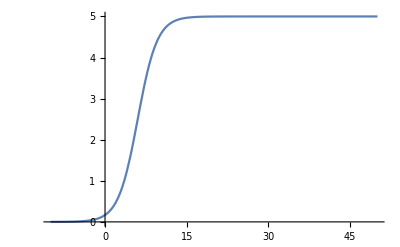

```mathematica
Plot[S[x], {x,-10,50}]
```

```mathematica
S[-5600]
```

0.208232

```mathematica
D[S[u], u]
```

(2.8 ⅇ^(0.56 (6-u)))/((1+ⅇ^(0.56 (6-u)))^2)

```mathematica
DSolve[system,{y0,y1},{x}]
```

DSolve[{p'[x]==1,q'[x]==x,True,s'[x]==(0.56[x])/(p[x]+4 0.56[x] q[x])},{y0,y1},{x}]

```mathematica
system{
x0'[t]=y0[t],
y0'[t]=A*a*S[upy[t]]-2*a*y0[t]-a^2*x0[t],
x1'[t]=y1[t],
y1'[t]=A*a*(1/C2+S[uex[t]])-2*a*y1[t]-a^2*x1[t],
x2'[t]=y2[t],
y2'[t]=B*b*S[uis[t]] -2*b*y2[t]-b^2*x2[t],
x3'[t]=y3[t],
y3'[t]=G*g*S[uif[t]]-2*g*y3[t]-g^2*x3[t],
upy[t]=C2*x1[t]-C4*x2[t]-C7*x3[t],
uex[t]=C1*x0[t],
uis[t]=C3*x0[t],
uif[t]=C5*x0[t]-C6*x2[t]
}
```

{p'[x]==1,q'[x]==x,True,s'[x]==(0.56[x])/(p[x]+4 0.56[x] q[x])} {y0,(0.01625 s)/(1+ⅇ^(0.56 (6-0.8 C x1+0.25 C x2+0.8 C x3)))-10000 x0-200 y0,y1,0.325 (1.25/C+5./(1+ⅇ^(0.56 (6-C x0))))-10000 x1-200 y1,y2,5.5/(1+ⅇ^(0.56 (6-0.25 C x0)))-2500 x2-100 y2,y3,25./(1+ⅇ^(0.56 (6-0.3 C x0+0.1 C x2)))-250000 x3-1000 y3,0.8 C x1-0.25 C x2-0.8 C x3,C x0,0.25 C x0,0.3 C x0-0.1 C x2}